```mathematica
Clear[Lx,Ly,A,B,
sx2d,SX2D,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=32;
Ly=32;
midPtX = Floor[Lx/2];
midPtY = Floor[Ly/2];
A=Lx*Ly;
Lz=20;
```

```mathematica
B=0.5;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]
Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2 Exp[- I B],sy2d[(k+1)Lx+j,k Lx+j]=I/2 Exp[ I B]},{j,midPtX+1,Lx}],{k,midPtY,midPtY}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]
Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2 Exp[- I B],cy2d[(k+1)Lx+j,k Lx+j]=1/2 Exp[I B]},{j,midPtX+1,Lx}],{k,midPtY,midPtY}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM1]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianWSM1[t_,t0_,m_,tz_,kz_, αy_]:=t*(KroneckerProduct[SX2D,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+KroneckerProduct[2*Cons-t0*(CX2D+CY2D+αy*CY2DP),σ3]+KroneckerProduct[(tz *Cos[kz]-m)*Cons,σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange,β]
```

```mathematica
β=-1.75;
```

```mathematica
{val,vec}=Eigensystem[HamiltonianWSM1[1.,1.,0,1,(β π)/2,0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

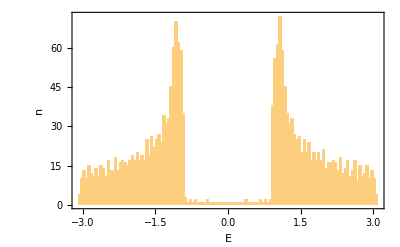

```mathematica
Show[Histogram[val,100],PlotRange-> All, Frame-> True, FrameLabel-> {"E","n"},BaseStyle-> 16,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[kzVector]
```

```mathematica
kzVector = N@Subdivide[-π,π,Lz-1]
```

{-3.14159,-2.8109,-2.4802,-2.14951,-1.81882,-1.48812,-1.15743,-0.826735,-0.496041,-0.165347,0.165347,0.496041,0.826735,1.15743,1.48812,1.81882,2.14951,2.4802,2.8109,3.14159}

```mathematica
NumPoints=Dimensions[kzVector][[1]]
```

20

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[SitesWithMagFieldInside,Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

2048

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
SitesWithMagFieldInside = {{midPtX,midPtY},{midPtX+1,midPtY},{midPtX+1,midPtY+1},{midPtX,midPtY+1},{midPtX,midPtY}};
```

```mathematica
SitesSummedOver ={{midPtX-1,1},{midPtX+2,1},{midPtX+2,Ly},{midPtX-1,Ly},{midPtX-1,1}};
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=(2/(1+Sqrt[5]))*(x-1)+8.5
LineDn[x_]:=(2/(1+Sqrt[5]))*(x-2)+6
```

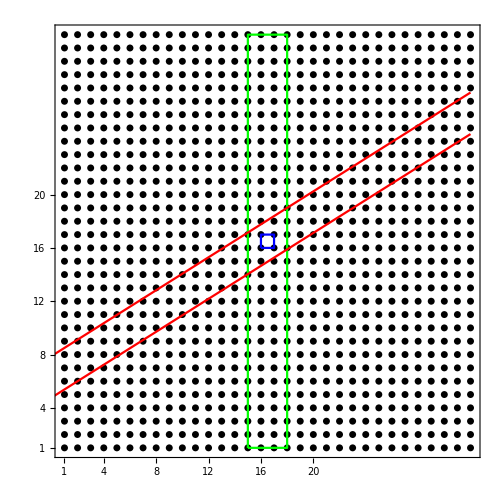

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
ListPlot[SitesWithMagFieldInside,PlotStyle-> {Blue,PointSize[0.01]},Joined-> True],
ListPlot[SitesSummedOver,PlotStyle-> {Green,PointSize[0.01]},Joined-> True],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew]
```

{161,193,194,195,225,226,227,228,229,258,259,260,261,262,292,293,294,295,296,326,327,328,329,330,359,360,361,362,363,393,394,395,396,397,426,427,428,429,430,460,461,462,463,464,494,495,496,497,498,527,528,529,530,531,561,562,563,564,565,594,595,596,597,598,599,628,629,630,631,632,662,663,664,665,666,695,696,697,698,699,729,730,731,732,733,763,764,765,766,767,796,797,798,799,800,830,831,832,863,864}

```mathematica
(** Fibonup2={}; **)
```

```mathematica
(** Do[Do[Fibonup2=Append[Fibonup2,x+(y-1)*Lx],{y,6,15}],{x,6,15}]**)
```

```mathematica
(** Fibonup2**)
```

```mathematica
(** Clear[Fibonup]**)
```

```mathematica
(** Fibonup = Fibonup2**)
```

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
(**--Compare with the previous (manually calculated) Fibonup for 20x20 sites--**)
```

```mathematica
(**--Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};--**)
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
(**-- Fibondown=Table[Fibonlist[[j]]+A,{j,1,Dimensions[Fibonlist][[1]]}]; --**)
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon]
```

{321,322,385,386,387,388,389,390,449,450,451,452,453,454,455,456,457,458,515,516,517,518,519,520,521,522,523,524,583,584,585,586,587,588,589,590,591,592,651,652,653,654,655,656,657,658,659,660,717,718,719,720,721,722,723,724,725,726,785,786,787,788,789,790,791,792,793,794,851,852,853,854,855,856,857,858,859,860,919,920,921,922,923,924,925,926,927,928,987,988,989,990,991,992,993,994,995,996,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1457,1458,1459,1460,1461,1462,1463,1464,1465,1466,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1591,1592,1593,1594,1595,1596,1597,1598,1599,1600,1659,1660,1661,1662,1663,1664,1725,1726,1727,1728}

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

200

```mathematica
NOrbitalsQuasi/2
```

100

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

1848

```mathematica
PercentageDataIn = N[NOrbitalsQuasi/(2*A)]
```

0.0976563

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{2048}

```mathematica
(**-- a=F1;
Do[
a=Drop[a,{TotalFibon[[NOrbitalsQuasi-i]]}],
{i,0,NOrbitalsQuasi-1,1}
] --**)
```

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(** Mixed boundary **)
```

```mathematica
(** Clear[bb];
bb={};
Do[{Clear[aa],
aa=Eigenvalues[HamiltonianWSM1[1,1,0,1,kzVector[[i]],1]],
Do[bb=Append[bb,{kzVector[[i]],aa[[j]]}],{j,1,2*A}]},{i,1,NumPoints}] **)
```

```mathematica
(** bb = Sort[Re[bb]]; **)
```

```mathematica
(** Show[ListPlot[bb,PlotRange-> { {-2.5,-1} ,{-0.5,0.5}},PlotStyle->PointSize[0.03]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

```mathematica
(** Plot1=Show[ListPlot[bb,PlotRange-> { {-3.14,3.14} ,{-2,2}},PlotStyle->{PointSize[0.01],Black}],FrameLabel-> {"kz","Energy"},BaseStyle-> 18,Frame-> True,FrameTicks-> {{-π,-π/2,0,π/2,π},Automatic,{},{}}] **)
```

```mathematica
(** Calculate Charge density as a function of position **)
```

```mathematica
Clear[ChargeXY, ChargeXYFlatten, ChargeXYPlot]
```

```mathematica
ChargeXY = Table[{x,y,0},{x,1,Lx},{y,1,Ly}];
```

```mathematica
Dimensions[ChargeXY]
```

{32,32,3}

```mathematica
Do[{Clear[HTrial,ValueFibon,VecFibon,ValVecFibon,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D],
HTrial =HamiltonianWSM1[1,1,0,1,kzVector[[kzIndex]],1],
(*---------------------------------------------------------*)
Hfbfb[i_Integer,j_Integer]=0,
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
],
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}],
(*---------------------------------------------------------*)
H2d2d[i_Integer,j_Integer]=0,
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
],
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}],
(*------------------------------------------------------*)
H2dfb[i_Integer,j_Integer]=0,

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
],
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}],
(*-------------------------------------------------*)
Hfb2d[i_Integer,j_Integer]=0,

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
],
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}],

(*---------------------------------------------------------------------------------------------------------------------------------*)
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon],
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB),
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor],
ValVecFibon=SortBy[Transpose[{Re[ValueFibon],VecFibon}],First],
Do[Do[{Clear[x,y],x=XList[[n]],y=YList[[n]],ChargeXY[[x,y]][[3]] += Abs[ValVecFibon[[J,2,2n]]]^2+Abs[ValVecFibon[[J,2,2n-1]]]^2},{n,1,NOrbitalsQuasi/2}],{J,1,NOrbitalsQuasi/2}]},{kzIndex ,1,Lz}];
```

$Aborted

```mathematica
ChargeXY;
```

```mathematica
ChargeXYFlatten = Flatten[ChargeXY];
```

```mathematica
Dimensions[ChargeXYFlatten][[1]]
```

3072

```mathematica
Lx*Ly*3
```

3072

```mathematica
ChargeXYFlatten[[18]]
```

18.6074

```mathematica
ChargeXYPlot = Table[{ChargeXYFlatten[[3i-2]],ChargeXYFlatten[[3i-1]],ChargeXYFlatten[[3i]]},{i,1,Dimensions[ChargeXYFlatten][[1]]/3}]
```

{{1,1,0},{1,2,0},{1,3,0},{1,4,0},{1,5,0},{1,6,18.6074},{1,7,18.6074},{1,8,18.6074},{1,9,0},{1,10,0},{1,11,0},{1,12,0},{1,13,0},{1,14,0},{1,15,0},{1,16,0},{1,17,0},{1,18,0},{1,19,0},{1,20,0},{1,21,0},{1,22,0},{1,23,0},{1,24,0},{1,25,0},{1,26,0},{1,27,0},{1,28,0},{1,29,0},{1,30,0},{1,31,0},{1,32,0},{2,1,0},{2,2,0},{2,3,0},{2,4,0},{2,5,0},{2,6,0},{2,7,19.8488},{2,8,19.8488},{2,9,19.8488},{2,10,0},{2,11,0},{2,12,0},{2,13,0},{2,14,0},{2,15,0},{2,16,0},{2,17,0},{2,18,0},{2,19,0},{2,20,0},{2,21,0},{2,22,0},{2,23,0},{2,24,0},{2,25,0},{2,26,0},{2,27,0},{2,28,0},{2,29,0},{2,30,0},{2,31,0},{2,32,0},{3,1,0},{3,2,0},{3,3,0},{3,4,0},{3,5,0},{3,6,0},{3,7,19.9417},{3,8,19.9417},{3,9,19.9417},{3,10,0},{3,11,0},{3,12,0},{3,13,0},{3,14,0},{3,15,0},{3,16,0},{3,17,0},{3,18,0},{3,19,0},{3,20,0},{3,21,0},{3,22,0},{3,23,0},{3,24,0},{3,25,0},{3,26,0},{3,27,0},{3,28,0},{3,29,0},{3,30,0},{3,31,0},{3,32,0},{4,1,0},{4,2,0},{4,3,0},{4,4,0},{4,5,0},{4,6,0},{4,7,0},{4,8,19.9712},{4,9,19.9711},{4,10,19.9711},{4,11,0},{4,12,0},{4,13,0},{4,14,0},{4,15,0},{4,16,0},{4,17,0},{4,18,0},{4,19,0},{4,20,0},{4,21,0},{4,22,0},{4,23,0},{4,24,0},{4,25,0},{4,26,0},{4,27,0},{4,28,0},{4,29,0},{4,30,0},{4,31,0},{4,32,0},{5,1,0},{5,2,0},{5,3,0},{5,4,0},{5,5,0},{5,6,0},{5,7,0},{5,8,19.9844},{5,9,19.9844},{5,10,19.9844},{5,11,0},{5,12,0},{5,13,0},{5,14,0},{5,15,0},{5,16,0},{5,17,0},{5,18,0},{5,19,0},{5,20,0},{5,21,0},{5,22,0},{5,23,0},{5,24,0},{5,25,0},{5,26,0},{5,27,0},{5,28,0},{5,29,0},{5,30,0},{5,31,0},{5,32,0},{6,1,0},{6,2,0},{6,3,0},{6,4,0},{6,5,0},{6,6,0},{6,7,0},{6,8,0},{6,9,19.9912},{6,10,19.9912},{6,11,19.9912},{6,12,0},{6,13,0},{6,14,0},{6,15,0},{6,16,0},{6,17,0},{6,18,0},{6,19,0},{6,20,0},{6,21,0},{6,22,0},{6,23,0},{6,24,0},{6,25,0},{6,26,0},{6,27,0},{6,28,0},{6,29,0},{6,30,0},{6,31,0},{6,32,0},{7,1,0},{7,2,0},{7,3,0},{7,4,0},{7,5,0},{7,6,0},{7,7,0},{7,8,0},{7,9,0},{7,10,19.995},{7,11,19.995},{7,12,19.995},{7,13,0},{7,14,0},{7,15,0},{7,16,0},{7,17,0},{7,18,0},{7,19,0},{7,20,0},{7,21,0},{7,22,0},{7,23,0},{7,24,0},{7,25,0},{7,26,0},{7,27,0},{7,28,0},{7,29,0},{7,30,0},{7,31,0},{7,32,0},{8,1,0},{8,2,0},{8,3,0},{8,4,0},{8,5,0},{8,6,0},{8,7,0},{8,8,0},{8,9,0},{8,10,19.9971},{8,11,19.9971},{8,12,19.9971},{8,13,0},{8,14,0},{8,15,0},{8,16,0},{8,17,0},{8,18,0},{8,19,0},{8,20,0},{8,21,0},{8,22,0},{8,23,0},{8,24,0},{8,25,0},{8,26,0},{8,27,0},{8,28,0},{8,29,0},{8,30,0},{8,31,0},{8,32,0},{9,1,0},{9,2,0},{9,3,0},{9,4,0},{9,5,0},{9,6,0},{9,7,0},{9,8,0},{9,9,0},{9,10,0},{9,11,19.9982},{9,12,19.9982},{9,13,19.9982},{9,14,0},{9,15,0},{9,16,0},{9,17,0},{9,18,0},{9,19,0},{9,20,0},{9,21,0},{9,22,0},{9,23,0},{9,24,0},{9,25,0},{9,26,0},{9,27,0},{9,28,0},{9,29,0},{9,30,0},{9,31,0},{9,32,0},{10,1,0},{10,2,0},{10,3,0},{10,4,0},{10,5,0},{10,6,0},{10,7,0},{10,8,0},{10,9,0},{10,10,0},{10,11,19.9989},{10,12,19.9989},{10,13,19.9989},{10,14,19.9988},{10,15,0},{10,16,0},{10,17,0},{10,18,0},{10,19,0},{10,20,0},{10,21,0},{10,22,0},{10,23,0},{10,24,0},{10,25,0},{10,26,0},{10,27,0},{10,28,0},{10,29,0},{10,30,0},{10,31,0},{10,32,0},{11,1,0},{11,2,0},{11,3,0},{11,4,0},{11,5,0},{11,6,0},{11,7,0},{11,8,0},{11,9,0},{11,10,0},{11,11,0},{11,12,19.9992},{11,13,19.9992},{11,14,19.9992},{11,15,0},{11,16,0},{11,17,0},{11,18,0},{11,19,0},{11,20,0},{11,21,0},{11,22,0},{11,23,0},{11,24,0},{11,25,0},{11,26,0},{11,27,0},{11,28,0},{11,29,0},{11,30,0},{11,31,0},{11,32,0},{12,1,0},{12,2,0},{12,3,0},{12,4,0},{12,5,0},{12,6,0},{12,7,0},{12,8,0},{12,9,0},{12,10,0},{12,11,0},{12,12,0},{12,13,19.9994},{12,14,19.9994},{12,15,19.9994},{12,16,0},{12,17,0},{12,18,0},{12,19,0},{12,20,0},{12,21,0},{12,22,0},{12,23,0},{12,24,0},{12,25,0},{12,26,0},{12,27,0},{12,28,0},{12,29,0},{12,30,0},{12,31,0},{12,32,0},{13,1,0},{13,2,0},{13,3,0},{13,4,0},{13,5,0},{13,6,0},{13,7,0},{13,8,0},{13,9,0},{13,10,0},{13,11,0},{13,12,0},{13,13,19.9995},{13,14,19.9995},{13,15,19.9996},{13,16,0},{13,17,0},{13,18,0},{13,19,0},{13,20,0},{13,21,0},{13,22,0},{13,23,0},{13,24,0},{13,25,0},{13,26,0},{13,27,0},{13,28,0},{13,29,0},{13,30,0},{13,31,0},{13,32,0},{14,1,0},{14,2,0},{14,3,0},{14,4,0},{14,5,0},{14,6,0},{14,7,0},{14,8,0},{14,9,0},{14,10,0},{14,11,0},{14,12,0},{14,13,0},{14,14,19.9996},{14,15,19.9999},{14,16,20.0005},{14,17,0},{14,18,0},{14,19,0},{14,20,0},{14,21,0},{14,22,0},{14,23,0},{14,24,0},{14,25,0},{14,26,0},{14,27,0},{14,28,0},{14,29,0},{14,30,0},{14,31,0},{14,32,0},{15,1,0},{15,2,0},{15,3,0},{15,4,0},{15,5,0},{15,6,0},{15,7,0},{15,8,0},{15,9,0},{15,10,0},{15,11,0},{15,12,0},{15,13,0},{15,14,0},{15,15,20.0005},{15,16,20.0029},{15,17,20.0292},{15,18,0},{15,19,0},{15,20,0},{15,21,0},{15,22,0},{15,23,0},{15,24,0},{15,25,0},{15,26,0},{15,27,0},{15,28,0},{15,29,0},{15,30,0},{15,31,0},{15,32,0},{16,1,0},{16,2,0},{16,3,0},{16,4,0},{16,5,0},{16,6,0},{16,7,0},{16,8,0},{16,9,0},{16,10,0},{16,11,0},{16,12,0},{16,13,0},{16,14,0},{16,15,20.0029},{16,16,20.0195},{16,17,20.2791},{16,18,0},{16,19,0},{16,20,0},{16,21,0},{16,22,0},{16,23,0},{16,24,0},{16,25,0},{16,26,0},{16,27,0},{16,28,0},{16,29,0},{16,30,0},{16,31,0},{16,32,0},{17,1,0},{17,2,0},{17,3,0},{17,4,0},{17,5,0},{17,6,0},{17,7,0},{17,8,0},{17,9,0},{17,10,0},{17,11,0},{17,12,0},{17,13,0},{17,14,0},{17,15,0},{17,16,20.0189},{17,17,20.2768},{17,18,20.2802},{17,19,0},{17,20,0},{17,21,0},{17,22,0},{17,23,0},{17,24,0},{17,25,0},{17,26,0},{17,27,0},{17,28,0},{17,29,0},{17,30,0},{17,31,0},{17,32,0},{18,1,0},{18,2,0},{18,3,0},{18,4,0},{18,5,0},{18,6,0},{18,7,0},{18,8,0},{18,9,0},{18,10,0},{18,11,0},{18,12,0},{18,13,0},{18,14,0},{18,15,0},{18,16,20.0027},{18,17,20.0191},{18,18,20.0195},{18,19,20.0029},{18,20,0},{18,21,0},{18,22,0},{18,23,0},{18,24,0},{18,25,0},{18,26,0},{18,27,0},{18,28,0},{18,29,0},{18,30,0},{18,31,0},{18,32,0},{19,1,0},{19,2,0},{19,3,0},{19,4,0},{19,5,0},{19,6,0},{19,7,0},{19,8,0},{19,9,0},{19,10,0},{19,11,0},{19,12,0},{19,13,0},{19,14,0},{19,15,0},{19,16,0},{19,17,20.0027},{19,18,20.0029},{19,19,20.0007},{19,20,0},{19,21,0},{19,22,0},{19,23,0},{19,24,0},{19,25,0},{19,26,0},{19,27,0},{19,28,0},{19,29,0},{19,30,0},{19,31,0},{19,32,0},{20,1,0},{20,2,0},{20,3,0},{20,4,0},{20,5,0},{20,6,0},{20,7,0},{20,8,0},{20,9,0},{20,10,0},{20,11,0},{20,12,0},{20,13,0},{20,14,0},{20,15,0},{20,16,0},{20,17,0},{20,18,20.0005},{20,19,20.0001},{20,20,20.},{20,21,0},{20,22,0},{20,23,0},{20,24,0},{20,25,0},{20,26,0},{20,27,0},{20,28,0},{20,29,0},{20,30,0},{20,31,0},{20,32,0},{21,1,0},{21,2,0},{21,3,0},{21,4,0},{21,5,0},{21,6,0},{21,7,0},{21,8,0},{21,9,0},{21,10,0},{21,11,0},{21,12,0},{21,13,0},{21,14,0},{21,15,0},{21,16,0},{21,17,0},{21,18,20.0001},{21,19,20.0001},{21,20,20.},{21,21,0},{21,22,0},{21,23,0},{21,24,0},{21,25,0},{21,26,0},{21,27,0},{21,28,0},{21,29,0},{21,30,0},{21,31,0},{21,32,0},{22,1,0},{22,2,0},{22,3,0},{22,4,0},{22,5,0},{22,6,0},{22,7,0},{22,8,0},{22,9,0},{22,10,0},{22,11,0},{22,12,0},{22,13,0},{22,14,0},{22,15,0},{22,16,0},{22,17,0},{22,18,0},{22,19,20.0002},{22,20,20.0002},{22,21,20.0002},{22,22,0},{22,23,0},{22,24,0},{22,25,0},{22,26,0},{22,27,0},{22,28,0},{22,29,0},{22,30,0},{22,31,0},{22,32,0},{23,1,0},{23,2,0},{23,3,0},{23,4,0},{23,5,0},{23,6,0},{23,7,0},{23,8,0},{23,9,0},{23,10,0},{23,11,0},{23,12,0},{23,13,0},{23,14,0},{23,15,0},{23,16,0},{23,17,0},{23,18,0},{23,19,20.0005},{23,20,20.0006},{23,21,20.0006},{23,22,20.0006},{23,23,0},{23,24,0},{23,25,0},{23,26,0},{23,27,0},{23,28,0},{23,29,0},{23,30,0},{23,31,0},{23,32,0},{24,1,0},{24,2,0},{24,3,0},{24,4,0},{24,5,0},{24,6,0},{24,7,0},{24,8,0},{24,9,0},{24,10,0},{24,11,0},{24,12,0},{24,13,0},{24,14,0},{24,15,0},{24,16,0},{24,17,0},{24,18,0},{24,19,0},{24,20,20.0012},{24,21,20.0013},{24,22,20.0012},{24,23,0},{24,24,0},{24,25,0},{24,26,0},{24,27,0},{24,28,0},{24,29,0},{24,30,0},{24,31,0},{24,32,0},{25,1,0},{25,2,0},{25,3,0},{25,4,0},{25,5,0},{25,6,0},{25,7,0},{25,8,0},{25,9,0},{25,10,0},{25,11,0},{25,12,0},{25,13,0},{25,14,0},{25,15,0},{25,16,0},{25,17,0},{25,18,0},{25,19,0},{25,20,0},{25,21,20.0022},{25,22,20.0023},{25,23,20.0022},{25,24,0},{25,25,0},{25,26,0},{25,27,0},{25,28,0},{25,29,0},{25,30,0},{25,31,0},{25,32,0},{26,1,0},{26,2,0},{26,3,0},{26,4,0},{26,5,0},{26,6,0},{26,7,0},{26,8,0},{26,9,0},{26,10,0},{26,11,0},{26,12,0},{26,13,0},{26,14,0},{26,15,0},{26,16,0},{26,17,0},{26,18,0},{26,19,0},{26,20,0},{26,21,20.004},{26,22,20.0042},{26,23,20.004},{26,24,0},{26,25,0},{26,26,0},{26,27,0},{26,28,0},{26,29,0},{26,30,0},{26,31,0},{26,32,0},{27,1,0},{27,2,0},{27,3,0},{27,4,0},{27,5,0},{27,6,0},{27,7,0},{27,8,0},{27,9,0},{27,10,0},{27,11,0},{27,12,0},{27,13,0},{27,14,0},{27,15,0},{27,16,0},{27,17,0},{27,18,0},{27,19,0},{27,20,0},{27,21,0},{27,22,20.007},{27,23,20.0072},{27,24,20.0071},{27,25,0},{27,26,0},{27,27,0},{27,28,0},{27,29,0},{27,30,0},{27,31,0},{27,32,0},{28,1,0},{28,2,0},{28,3,0},{28,4,0},{28,5,0},{28,6,0},{28,7,0},{28,8,0},{28,9,0},{28,10,0},{28,11,0},{28,12,0},{28,13,0},{28,14,0},{28,15,0},{28,16,0},{28,17,0},{28,18,0},{28,19,0},{28,20,0},{28,21,0},{28,22,0},{28,23,20.0122},{28,24,20.0122},{28,25,20.0119},{28,26,0},{28,27,0},{28,28,0},{28,29,0},{28,30,0},{28,31,0},{28,32,0},{29,1,0},{29,2,0},{29,3,0},{29,4,0},{29,5,0},{29,6,0},{29,7,0},{29,8,0},{29,9,0},{29,10,0},{29,11,0},{29,12,0},{29,13,0},{29,14,0},{29,15,0},{29,16,0},{29,17,0},{29,18,0},{29,19,0},{29,20,0},{29,21,0},{29,22,0},{29,23,20.0227},{29,24,20.0225},{29,25,20.0218},{29,26,0},{29,27,0},{29,28,0},{29,29,0},{29,30,0},{29,31,0},{29,32,0},{30,1,0},{30,2,0},{30,3,0},{30,4,0},{30,5,0},{30,6,0},{30,7,0},{30,8,0},{30,9,0},{30,10,0},{30,11,0},{30,12,0},{30,13,0},{30,14,0},{30,15,0},{30,16,0},{30,17,0},{30,18,0},{30,19,0},{30,20,0},{30,21,0},{30,22,0},{30,23,0},{30,24,20.0434},{30,25,20.0429},{30,26,20.0427},{30,27,0},{30,28,0},{30,29,0},{30,30,0},{30,31,0},{30,32,0},{31,1,0},{31,2,0},{31,3,0},{31,4,0},{31,5,0},{31,6,0},{31,7,0},{31,8,0},{31,9,0},{31,10,0},{31,11,0},{31,12,0},{31,13,0},{31,14,0},{31,15,0},{31,16,0},{31,17,0},{31,18,0},{31,19,0},{31,20,0},{31,21,0},{31,22,0},{31,23,0},{31,24,20.1093},{31,25,20.1072},{31,26,20.1092},{31,27,20.1052},{31,28,0},{31,29,0},{31,30,0},{31,31,0},{31,32,0},{32,1,0},{32,2,0},{32,3,0},{32,4,0},{32,5,0},{32,6,0},{32,7,0},{32,8,0},{32,9,0},{32,10,0},{32,11,0},{32,12,0},{32,13,0},{32,14,0},{32,15,0},{32,16,0},{32,17,0},{32,18,0},{32,19,0},{32,20,0},{32,21,0},{32,22,0},{32,23,0},{32,24,0},{32,25,21.1104},{32,26,21.1087},{32,27,21.1152},{32,28,0},{32,29,0},{32,30,0},{32,31,0},{32,32,0}}

```mathematica
ChargeXYPlotData = Table[ChargeXYFlatten[[3i]],{i,1,Dimensions[ChargeXYFlatten][[1]]/3}]
```

{0,0,0,0,0,18.6074,18.6074,18.6074,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19.8488,19.8488,19.8488,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19.9417,19.9417,19.9417,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19.9712,19.9711,19.9711,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19.9844,19.9844,19.9844,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19.9912,19.9912,19.9912,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19.995,19.995,19.995,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19.9971,19.9971,19.9971,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19.9982,19.9982,19.9982,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19.9989,19.9989,19.9989,19.9988,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19.9992,19.9992,19.9992,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19.9994,19.9994,19.9994,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19.9995,19.9995,19.9996,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19.9996,19.9999,20.0005,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.0005,20.0029,20.0292,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.0029,20.0195,20.2791,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.0189,20.2768,20.2802,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.0027,20.0191,20.0195,20.0029,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.0027,20.0029,20.0007,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.0005,20.0001,20.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.0001,20.0001,20.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.0002,20.0002,20.0002,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.0005,20.0006,20.0006,20.0006,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.0012,20.0013,20.0012,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.0022,20.0023,20.0022,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.004,20.0042,20.004,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.007,20.0072,20.0071,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.0122,20.0122,20.0119,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.0227,20.0225,20.0218,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.0434,20.0429,20.0427,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20.1093,20.1072,20.1092,20.1052,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,21.1104,21.1087,21.1152,0,0,0,0,0}

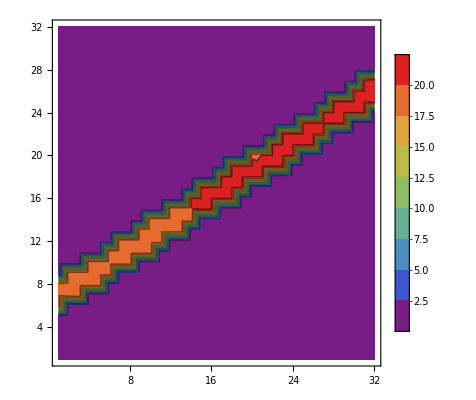

```mathematica
ListContourPlot[ChargeXYPlot,PlotRange->{{1,Lx},{1,Ly}},PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

```mathematica
ListPlot3D[ChargeXYPlot,PlotRange->{{1,Lx},{1,Ly}},PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
(** to measure in the unit of e/π, we multiply with π **)
```

```mathematica
deltaQ = π * Sum[(ChargeXY[[x,y]][[3]])/Lz,{x,midPtX-1,midPtX+2},{y,1,Ly}]
```

40.9905

```mathematica
B
```

0.6

```mathematica
phiOverPhi0 = N[B/(2*π)]
```

0.095493

```mathematica
(** This data is 32x32 systems, with phi divided by phi_0 **)
```

```mathematica
dataQ32x32 = {{0,40.8407044966674},{0.015915494309189534, 40.86570997583451},{0.03183098861837907,40.890708309278985},{0.06366197723675814,40.940669512401385},{0.09549296585513721,40.99054894460834}}
```

{{0,40.8407},{0.0159155,40.8657},{0.031831,40.8907},{0.063662,40.9407}}

```mathematica
(** These are old results for 16x16 systems **)
```

```mathematica
(** This is for the four sites and one extra in the quasicrystal WITHOUT DIVIDING BY PHI_0**)
```

```mathematica
dataQ316x16 = {{0,15.707963267948996},{0.01,15.710214413907009},{0.02,15.712467541699205},{0.03,15.714721717819975},{0.04,15.716977397904165},{0.1,15.73055851050975}}
```

{{0,15.708},{0.01,15.7102},{0.02,15.7125},{0.03,15.7147},{0.04,15.717},{0.1,15.7306}}

```mathematica
(** This is for two more sites in left and right WITHOUT DIVIDING BY PHI_0**)
```

```mathematica
dataQ216x16 = {{0,50.265482457436626},{0.01,50.26780268583725},{0.02,50.27014384190568},{0.03,50.272487307954016},{0.04,50.27483408971736},{0.05,50.27718503476088},{0.07,50.28190187951746},{0.1,50.289018966548106},{0.3,50.33736411389633}}
```

{{0,50.2655},{0.01,50.2678},{0.02,50.2701},{0.03,50.2725},{0.04,50.2748},{0.05,50.2772},{0.07,50.2819},{0.1,50.289},{0.3,50.3374}}

```mathematica
(** This was the best data, taking one plucket in each side of the flux tube, summing over all y (but only values on quasicrystal are taken **)
```

```mathematica
(** WITHOUT DIVIDING BY PHI_0 **)
```

```mathematica
dataQ16x16 = {{0,31.415926535897874},{0.01, 31.41832339486044},{0.02,31.4207215414231},{0.03,31.423120632898538},{0.04,31.425521080509103},{0.05,31.427923230072782},{0.07,31.432733636444556},{0.1,31.65857326551975}}
```

{{0,31.4159},{0.01,31.4183},{0.02,31.4207},{0.03,31.4231},{0.04,31.4255},{0.05,31.4279},{0.07,31.4327},{0.1,31.6586}}

```mathematica
Dimensions[dataQ32x32][[1]]
```

4

```mathematica
(** Last value is off, so not taken **)
```

```mathematica
dataDeltaQ = Table[{dataQ32x32 [[i]][[1]],dataQ32x32 [[i]][[2]] - dataQ32x32[[1]][[2]]},{i,1,Dimensions[dataQ32x32 ][[1]]}]
```

{{0,0.},{0.0159155,0.0250055},{0.031831,0.0500038},{0.063662,0.099965}}

```mathematica
(** 32x32, plot phi/phi_0 -- upto 0.1, rational and irrational **)
```

```mathematica
(*** Older Slope when summed over one sets of sites in each side is 0.0239981 **)
```

```mathematica
slope = D[Fit[dataDeltaQ,{k},k],k]
```

1.57042

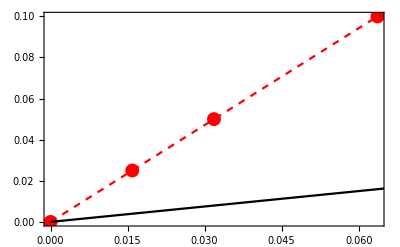

```mathematica
Show[ListPlot[dataDeltaQ,PlotStyle->{PointSize[0.025],Red}],Plot[slope * x,{x,0,0.3},PlotStyle->{Dashed,Red}],
Plot[π*x/2,{x,0,0.3},PlotStyle->Black],
Frame->True,BaseStyle->18,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```

```mathematica
N[slope/(π/2)]
```

0.999758

```mathematica
(** magnetic field 0.1 -> 64.04897097607557 **)
```

```mathematica
(** magnetic field 0.3 -> delta Q 64.14492972147679 **)
```

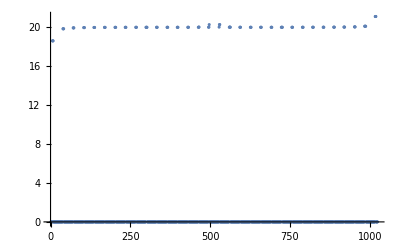

```mathematica
ListPlot[Transpose@{Table[i,{i,1,Lx*Ly}],ChargeXYPlotData},PlotRange->All]
```